```mathematica
Do[
MGD[j]=MeanGraphDistance[RandomGraph[WattsStrogatzGraphDistribution[5*j,0.3]]];
Print[MGD[j]];
,{j,1,100}]
```

1

8/5

66/35

214/95

178/75

1187/435

1569/595

737/260

3139/990

4064/1225

4892/1485

3032/885

711/208

8357/2415

10241/2775

12327/3160

4279/1190

15269/4005

3437/893

1061/275

1746/455

24591/5995

27128/6555

2077/510

31113/7750

34394/8385

38668/9045

40623/9730

∞

45844/11175

4679/1085

56891/12720

58171/13530

4908/1105

69458/15225

73229/16110

76661/17020

5426/1197

88238/18915

∞

15898/3485

100277/21945

106196/23005

18466/4015

57473/12600

24295/5267

126413/27495

27559/5736

140909/29890

10109/2075

30079/6477

165029/33670

168329/34980

34613/7263

36788/7535

93661/19530

100409/20235

208357/41905

211058/43365

109094/22425

115237/23180

16512/3193

80693/16485

52015/10208

263561/52650

3482/705

58067/11189

9799/1921

304063/59340

44942/8725

322366/62835

83873/16155

342159/66430

355087/68265

21394/4125

3901/758

381341/73920

402791/75855

410413/77815

4121/798

422989/81810

442333/83845

452384/85905

228013/43995

241833/45050

162352/30745

∞

260111/48290

103063/19758

∞

∞

282527/52785

577457/107880

588624/110215

601834/112575

2600/479

127335/23474

31222/5705

676798/122265

339099/62375

```mathematica
MGDdata=Table[{5*j,MGD[j]},{j,1,100}]
```

{{5,1},{10,8/5},{15,66/35},{20,214/95},{25,178/75},{30,1187/435},{35,1569/595},{40,737/260},{45,3139/990},{50,4064/1225},{55,4892/1485},{60,3032/885},{65,711/208},{70,8357/2415},{75,10241/2775},{80,12327/3160},{85,4279/1190},{90,15269/4005},{95,3437/893},{100,1061/275},{105,1746/455},{110,24591/5995},{115,27128/6555},{120,2077/510},{125,31113/7750},{130,34394/8385},{135,38668/9045},{140,40623/9730},{145,∞},{150,45844/11175},{155,4679/1085},{160,56891/12720},{165,58171/13530},{170,4908/1105},{175,69458/15225},{180,73229/16110},{185,76661/17020},{190,5426/1197},{195,88238/18915},{200,∞},{205,15898/3485},{210,100277/21945},{215,106196/23005},{220,18466/4015},{225,57473/12600},{230,24295/5267},{235,126413/27495},{240,27559/5736},{245,140909/29890},{250,10109/2075},{255,30079/6477},{260,165029/33670},{265,168329/34980},{270,34613/7263},{275,36788/7535},{280,93661/19530},{285,100409/20235},{290,208357/41905},{295,211058/43365},{300,109094/22425},{305,115237/23180},{310,16512/3193},{315,80693/16485},{320,52015/10208},{325,263561/52650},{330,3482/705},{335,58067/11189},{340,9799/1921},{345,304063/59340},{350,44942/8725},{355,322366/62835},{360,83873/16155},{365,342159/66430},{370,355087/68265},{375,21394/4125},{380,3901/758},{385,381341/73920},{390,402791/75855},{395,410413/77815},{400,4121/798},{405,422989/81810},{410,442333/83845},{415,452384/85905},{420,228013/43995},{425,241833/45050},{430,162352/30745},{435,∞},{440,260111/48290},{445,103063/19758},{450,∞},{455,∞},{460,282527/52785},{465,577457/107880},{470,588624/110215},{475,601834/112575},{480,2600/479},{485,127335/23474},{490,31222/5705},{495,676798/122265},{500,339099/62375}}

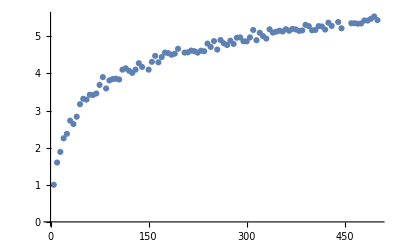

```mathematica
ListPlot[MGDdata]
```

```mathematica
LogMGDdata=Table[{Log[5*j],MGD[j]},{j,1,100}]
```

{{Log[5],1},{Log[10],8/5},{Log[15],66/35},{Log[20],214/95},{Log[25],178/75},{Log[30],1187/435},{Log[35],1569/595},{Log[40],737/260},{Log[45],3139/990},{Log[50],4064/1225},{Log[55],4892/1485},{Log[60],3032/885},{Log[65],711/208},{Log[70],8357/2415},{Log[75],10241/2775},{Log[80],12327/3160},{Log[85],4279/1190},{Log[90],15269/4005},{Log[95],3437/893},{Log[100],1061/275},{Log[105],1746/455},{Log[110],24591/5995},{Log[115],27128/6555},{Log[120],2077/510},{Log[125],31113/7750},{Log[130],34394/8385},{Log[135],38668/9045},{Log[140],40623/9730},{Log[145],∞},{Log[150],45844/11175},{Log[155],4679/1085},{Log[160],56891/12720},{Log[165],58171/13530},{Log[170],4908/1105},{Log[175],69458/15225},{Log[180],73229/16110},{Log[185],76661/17020},{Log[190],5426/1197},{Log[195],88238/18915},{Log[200],∞},{Log[205],15898/3485},{Log[210],100277/21945},{Log[215],106196/23005},{Log[220],18466/4015},{Log[225],57473/12600},{Log[230],24295/5267},{Log[235],126413/27495},{Log[240],27559/5736},{Log[245],140909/29890},{Log[250],10109/2075},{Log[255],30079/6477},{Log[260],165029/33670},{Log[265],168329/34980},{Log[270],34613/7263},{Log[275],36788/7535},{Log[280],93661/19530},{Log[285],100409/20235},{Log[290],208357/41905},{Log[295],211058/43365},{Log[300],109094/22425},{Log[305],115237/23180},{Log[310],16512/3193},{Log[315],80693/16485},{Log[320],52015/10208},{Log[325],263561/52650},{Log[330],3482/705},{Log[335],58067/11189},{Log[340],9799/1921},{Log[345],304063/59340},{Log[350],44942/8725},{Log[355],322366/62835},{Log[360],83873/16155},{Log[365],342159/66430},{Log[370],355087/68265},{Log[375],21394/4125},{Log[380],3901/758},{Log[385],381341/73920},{Log[390],402791/75855},{Log[395],410413/77815},{Log[400],4121/798},{Log[405],422989/81810},{Log[410],442333/83845},{Log[415],452384/85905},{Log[420],228013/43995},{Log[425],241833/45050},{Log[430],162352/30745},{Log[435],∞},{Log[440],260111/48290},{Log[445],103063/19758},{Log[450],∞},{Log[455],∞},{Log[460],282527/52785},{Log[465],577457/107880},{Log[470],588624/110215},{Log[475],601834/112575},{Log[480],2600/479},{Log[485],127335/23474},{Log[490],31222/5705},{Log[495],676798/122265},{Log[500],339099/62375}}

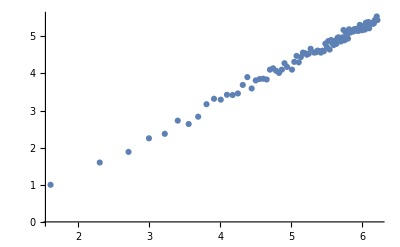

```mathematica
ListPlot[LogMGDdata]
```

```mathematica
kara={};
Do[If[TrueQ[Part[Part[LogMGDdata,j],2]!=∞],AppendTo[kara,Part[LogMGDdata,j]]];,
{j,1,100}];
```

```mathematica
logline=Fit[kara,{1,M},M]
```

-0.667907+0.985848 M

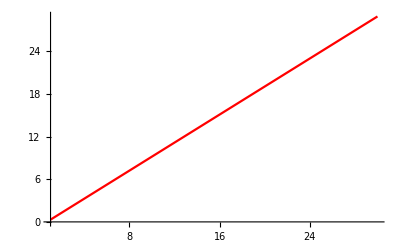

```mathematica
Plot[logline,{M,1,30},PlotStyle->Red]
```

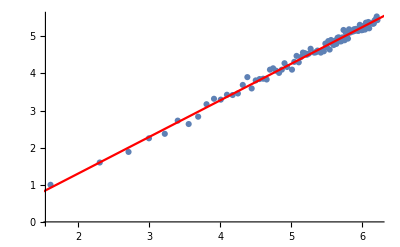

```mathematica
Show[ListPlot[LogMGDdata],Plot[logline,{M,1,30},PlotStyle->Red]]
```